```mathematica
e:=1
```

```mathematica
omega := 1
```

```mathematica
b:=1
```

```mathematica
r[t_]=-e/(omega b){Sin[omega t],Cos[omega t]}+{e/b,0}t+{0,e/(omega b)}
```

{t-Sin[t],1-Cos[t]}

```mathematica
r[t]//MatrixForm
```

(t-Sin[t]
1-Cos[t])

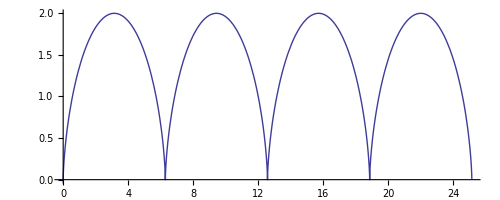

```mathematica
ParametricPlot[r[t],{t,0,25}]
```